Radiation beaming in the quantum regime

T. G. Blackburn, D. Seipt, S. S. Bulanov, and M. Marklund, 
PHYSICAL REVIEW A 101, 012505 (2020)

Notebook: Óscar Amaro,  2021 + June 2022,  @ GoLP-EPP

Introduction
Standard simulation of high energy electrons assumes photon emission is collinear with the parent particle’s trajectory. However, finite beaming effects can be relevant in some regimes.

## W^(3) triple differential photon emission rate

Here we plot this rate for different χ values and as a function of either θ or ω.

(u (-1-u+(1+(1+u)^2) z^(2/3)) BesselK[1/3,(2 u z)/(3 χ)])/(3 √3 π^2 (1+u)^3 χ)

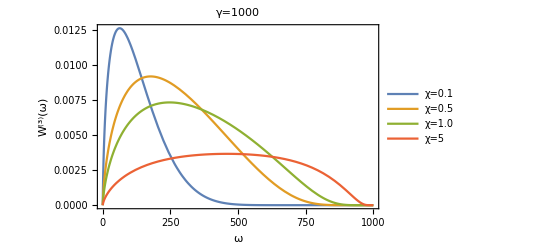

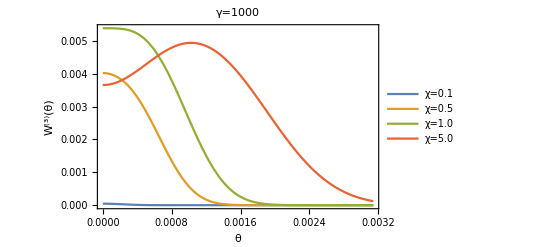

```mathematica
Clear[α,m,c,u,γ,ω,z,χ,β,W3,W3fun]
m =α=1;

(* equation 1 differential rate [29] V.N.Baier,V.M.Katkov,and V.M.Strakhovenko,Electro-magnetic Processes at High Energies in Oriented Single Crystals (World Scientific,Singapore,1998) *)
W3=(α m)/(3√3 π^2 χ)u/(1+u)^3(z^(2/3)(1+(1+u)^2)-(1+u))BesselK[1/3,(2 u z)/(3χ)]

(* replace definitions of u, z and β *)
W3//.{β->Sqrt[1-1/γ^2],u->ω/(γ-ω),z->(2γ^2(1-β Cos[θ]))^(3/2)};

W3fun[ω_?NumericQ, θ_?NumericQ, χ_?NumericQ,γ_?NumericQ]:=W3fun[ω,θ,χ,γ]=(m α ω BesselK[1/3,(4 √2 ω (γ^2 (1-√(1-1/γ^2) Cos[θ]))^(3/2))/(3 χ (γ-ω))] (-1-ω/(γ-ω)+2 (1+(1+ω/(γ-ω))^2) ((γ^2 (1-√(1-1/γ^2) Cos[θ]))^(3/2))^(2/3)))/(3 √3 π^2 χ (γ-ω) (1+ω/(γ-ω))^3);

γ1=1000;
(* W3 as a function of frequency *)
Plot[{W3fun[ω,0,0.1,γ1],W3fun[ω,0,0.5,γ1],W3fun[ω,0,1,γ1],W3fun[ω,0,5,γ1]},{ω,0,γ1},Frame->True,FrameLabel->{"ω","W^(3)(ω)"},PlotLegends->{"χ=0.1","χ=0.5","χ=1.0","χ=5"},PlotLabel->"γ=1000"]

(* W3 as a function of angle *)
Plot[{W3fun[γ1/2,θ,0.1,γ1],W3fun[γ1/2,θ,0.5,γ1],W3fun[γ1/2,θ,1,γ1],W3fun[γ1/2,θ,5,γ1]},{θ,0,π/γ1},Frame->True,FrameLabel->{"θ","W^(3)(θ)"},PlotLegends->{"χ=0.1","χ=0.5","χ=1.0","χ=5.0"},PlotLabel->"γ=1000"]
```

## <θ^2> mean-square angle of the power spectrum asymptotic expressions

To get the exact <θ^2>  as in the text, we need the Jacobian from du dz (ω,θ) to calculate the numerical integral. We then compare this with the asymptotic expressions.

```mathematica
Clear[γ,χ,β,u,z,θ]
β=Sqrt[1-1/γ^2];
u=ω/(γ-ω);
z=(2γ^2(1-β Cos[θ]))^(3/2);

(* (u,z) is a function of (ω,θ), so we need to calculate the determinant of this change of variables *)
Refine[Det[{{D[u,ω],D[u,θ]},{D[z,ω],D[z,θ]}}],{γ>0}]//Simplify
Clear[γ,χ,β,u,z,θ]
```

(3 √(2-2/γ^2) γ^4 √(1-√(1-1/γ^2) Cos[θ]) Sin[θ])/(γ-ω)^2

```mathematica
Clear[θ2,θmax]
θmax=0.1;
θ2[χ_,γ_]:=NIntegrate[( θ^2 ω W3fun[ω,θ,χ,γ] (3 √(2-2/γ^2) γ^4 √(1-√(1-1/γ^2) Cos[θ]) Sin[θ])/(γ-ω)^2),{θ,10^-12,θmax},{ω,0.00001γ,0.99999γ}]/NIntegrate[(  ω W3fun[ω,θ,χ,γ] (3 √(2-2/γ^2) γ^4 √(1-√(1-1/γ^2) Cos[θ]) Sin[θ])/(γ-ω)^2),{θ,10^-12,θmax},{ω,0.00001γ,0.99999γ}]//Quiet
```

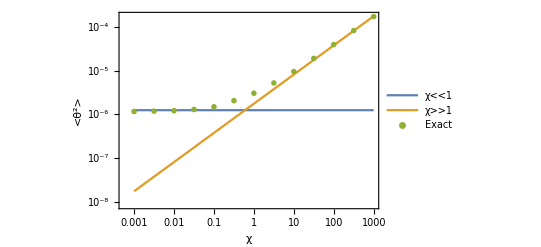

```mathematica
(* we then choose a fixed electron γ *)
γ=1000;
tab1=ParallelTable[{10^logχ,θ2[10^logχ,γ]//Quiet},{logχ,-3,3,0.5}];
tab1low=ParallelTable[{10^logχ,5/(4 γ^2)},{logχ,-3,3,0.1}];
tab1high=ParallelTable[{10^logχ,1.76/γ^2(10^logχ)^(2/3)},{logχ,-3,3,0.1}];
ListLogLogPlot[{tab1low,tab1high,tab1},Joined->{True,True,False},PlotLegends->{"χ<<1","χ>>1","Exact"},Frame->True,FrameLabel->{"χ","<θ^2>"},PlotMarkers->{None,None,"OpenMarkers"}]
```

## <θ^2> mean-square angle at fixed photon energy asymptotic expressions

We’ll justify the asymptotic expressions in equation 2. Since there’s a 1-to-1 relation between z and θ, we first need to invert this to perform the calculation of the integral, obtaining θ(z).

```mathematica
Clear[c,u,γ,ω,z,χ,β]
β=Sqrt[1-1/γ^2];
Solve[z==(2γ^2 (1-β Cos[θ]))^1.5,θ][[2,1,2]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ArcCos[(1. √(1.-1./γ^2) (-0.5 z^(2/3)+1. γ^2))/(-1.+1. γ^2)]

The domain of integration is determined by solving the limiting cases of the argument in ArcCos

```mathematica
Clear[γ,z]
Refine[Solve[(1. √(1.-1./γ^2) (-0.5 z^(2/3)+1. γ^2))/(-1.+1. γ^2)==1,z],{γ>1}]//Simplify
Refine[Solve[(1. √(1.-1./γ^2) (-0.5 z^(2/3)+1. γ^2))/(-1.+1. γ^2)==-1,z],{γ>1}]//Simplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{z→2.82843 (γ (1. γ+1. √(1/(-1.+1. γ^2))-1. γ^2 √(1/(-1.+1. γ^2))))^(3/2)}}

Solve::nongen: Solutions may not be valid for all values of parameters.

{{z→2.82843 (γ (1. γ-1. √(1/(-1.+1. γ^2))+1. γ^2 √(1/(-1.+1. γ^2))))^(3/2)}}

We now redefine the triple differential rate and integrate ∫θ(z)^2 W(z) dz / ∫ W(z) dz

```mathematica
Clear[γ,θ,u,z,χ,γ2θ2,tab2,tab2low,tab2high]
m =α=1;
γ2θ2[u_,χ_,γ_]:=NIntegrate[ (ArcCos[(1. √(1.-1./γ^2) (-0.5 z^(2/3)+1. γ^2))/(-1.+1. γ^2)])^2 (α m)/(3√3 π^2 χ)u/(1+u)^3(z^(2/3)(1+(1+u)^2)-(1+u))BesselK[1/3,(2 u z)/(3χ)],{z,2.8284271247461903 (γ (1. γ+1. √(1/(-1.+1. γ^2))-1. γ^2 √(1/(-1.+1. γ^2))))^(3/2),2.8284271247461903 (γ (1. γ-1. √(1/(-1.+1. γ^2))+1. γ^2 √(1/(-1.+1. γ^2))))^(3/2)},MinRecursion->9,AccuracyGoal->12]/NIntegrate[ (α m)/(3√3 π^2 χ)u/(1+u)^3(z^(2/3)(1+(1+u)^2)-(1+u))BesselK[1/3,(2 u z)/(3χ)],{z,2.8284271247461903 (γ (1. γ+1. √(1/(-1.+1. γ^2))-1. γ^2 √(1/(-1.+1. γ^2))))^(3/2),2.8284271247461903 (γ (1. γ-1. √(1/(-1.+1. γ^2))+1. γ^2 √(1/(-1.+1. γ^2))))^(3/2)},MinRecursion->9,AccuracyGoal->18,PrecisionGoal->18,WorkingPrecision->22]
```

Create table with “exact” result and asymptotic expressions.

```mathematica
γ=20;
u=1;
tab2=ParallelTable[{10^logχ,γ2θ2[u,10^logχ,γ]//Quiet},{logχ,-1,3,0.5}];
```

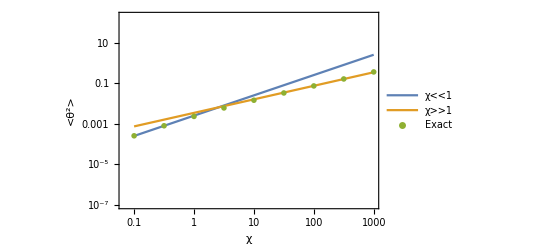

```mathematica
tab2high=ParallelTable[{10^logχ,1/γ^2 Gamma[4/3]/Gamma[2/3]((3 10^logχ)/u)^(2/3)},{logχ,-1,3,0.1}];
tab2low=ParallelTable[{10^logχ,1/γ^2(10^logχ/u)},{logχ,-1,3,0.1}];
ListLogLogPlot[{tab2low,tab2high,tab2},Joined->{True,True,False},PlotLegends->{"χ<<1","χ>>1","Exact"},Frame->True,FrameLabel->{"χ","<θ^2>"},PlotRange->{10^-7,200},PlotMarkers->{None,None,"OpenMarkers"}]
```

## Figure 3

I0 = 2 10^21 W/cm^2, ω = 1 MeV, γ = 500 MeV (m=0.511MeV)
λ = 0.8 μm , a0 = 0.855 Sqrt[I0/10^18]  λ[μm] , τ = 30 fs
χ = 2 γ a0 ω/m

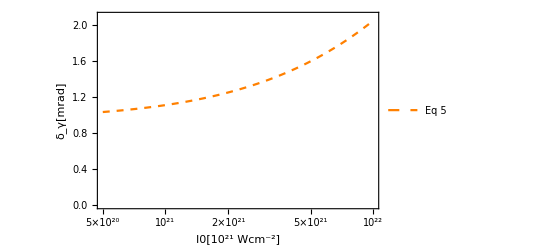

```mathematica
Clear[δ0,intg2,ω,τ,λ,I0,α,m,λμm,ωeV,γ0,δγ]
m=0.511 10^6;(*[eV]*)
γ0 = 500/m 10^6;(*[]*)
α=1/137;(*[]*)
λμm=0.8;(*[μm]*)
δ0=0.5 10^-3;(*[rad]*)
ω=2π 3 10^8/(λμm 10^-6);(*[s-1]*)
ωeV=ω 1.05 10^-34 /(9.11 10^-31 (3 10^8)^2) m; (*[eV]*)
τ=30 10^-15;(*[s]*)
intg2=ω τ Sqrt[π/(4Log[2])];(*[]*)
(* equation 5 *)
δγ[I0_]:=Sqrt[δ0^2 + (5(1+ℛ))/(8γ0^2)]//.{ℛ->(2α a0^2 γ0 ωeV)/(3m)intg2,a0->0.855Sqrt[I0/10^18]λμm}
LogLinearPlot[{10^3 δγ[I0]},{I0,0.5 10^21,10 10^21}, PlotLegends->{"Eq 5"},PlotStyle->{Orange,Dashed},Frame->True,FrameLabel->{"I0[10^21 Wcm^-2]","δ_γ[mrad]"},PlotRange->{0,2.1}]
```

## Electron-beam divergence: finite angle recoil Δp

<Δp>/m = 3√3 π ξ/40 for χ<<1 and 0.264 χ^1/3 for χ>>1

```mathematica
Clear[m ,α,γ,θ,u,z,χ,W3fun,Δp,tab3,tab3low,tab3high,θmax]
m =α=1;
θmax=0.1;
W3fun[ω_?NumericQ, θ_?NumericQ, χ_?NumericQ,γ_?NumericQ]:=W3fun[ω,θ,χ,γ]=(m α ω BesselK[1/3,(4 √2 ω (γ^2 (1-√(1-1/γ^2) Cos[θ]))^(3/2))/(3 χ (γ-ω))] (-1-ω/(γ-ω)+2 (1+(1+ω/(γ-ω))^2) ((γ^2 (1-√(1-1/γ^2) Cos[θ]))^(3/2))^(2/3)))/(3 √3 π^2 χ (γ-ω) (1+ω/(γ-ω))^3);
Δp[χ_,γ_]:=NIntegrate[( ω Sin[θ] W3fun[ω,θ,χ,γ] (3 √(2-2/γ^2) γ^4 √(1-√(1-1/γ^2) Cos[θ]) Sin[θ])/(γ-ω)^2),{θ,10^-12,θmax},{ω,0.00001γ,0.99999γ}]/NIntegrate[( W3fun[ω,θ,χ,γ] (3 √(2-2/γ^2) γ^4 √(1-√(1-1/γ^2) Cos[θ]) Sin[θ])/(γ-ω)^2),{θ,10^-12,θmax},{ω,0.00001γ,0.99999γ}]//Quiet
```

```mathematica
γ=20;
tab3=ParallelTable[{10^logχ,Δp[10^logχ,γ]//Quiet},{logχ,-2,3,0.5}];
```

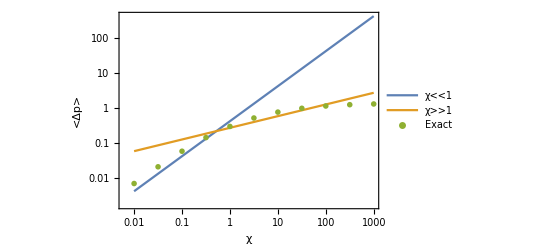

```mathematica
tab3high=ParallelTable[{10^logχ,0.264 (10^logχ)^(1/3)},{logχ,-2,3,0.1}];
tab3low=ParallelTable[{10^logχ,3√3 π/40 (10^logχ)},{logχ,-2,3,0.1}];
ListLogLogPlot[{tab3low,tab3high,tab3},Joined->{True,True,False},PlotLegends->{"χ<<1","χ>>1","Exact"},Frame->True,FrameLabel->{"χ","<Δp>"},PlotMarkers->{None,None,"OpenMarkers"}]
```

## Figure 5 : Effect of the transverse recoil on the electron angular distribution, in the collision of a 500-MeV electron beam and a linearly polarized laser pulse with peak intensity I0

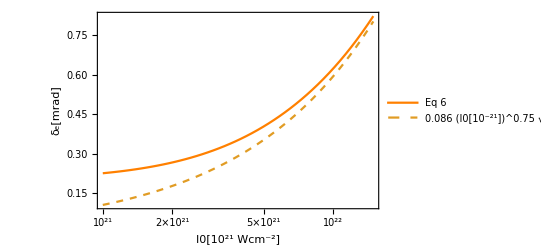

```mathematica
Clear[δ0,δe,intg3,ω,τ,λ,I0,α,m,λμm,ωeV]
m=0.511 10^6;(*[eV]*)
α=1/137;(*[]*)
λμm=0.4;(*[μm]*)
δ0=0.2 10^-3;(*[rad]*)
ω=2π 3 10^8/(λμm 10^-6);(*[s-1]*)
ωeV=ω 1.05 10^-34 /(9.11 10^-31 (3 10^8)^2) m; (*[eV]*)
τ=15 10^-15;(*[s]*)
intg3=ω τ Sqrt[π/(6Log[2])];(*[]*)
(* equation 6 *)
δe[I0_]:=Sqrt[δ0^2 + (26√3 α a0^3 ωeV^2)/(27π m^2)intg3]/.{a0->0.855Sqrt[I0/10^18]λμm}
(* approximate form *)
δeapp[I0_]:=0.086 (I0 10^-21)^0.75 Sqrt[τ/(10 10^-15)]
(* plot *)
LogLinearPlot[{10^3 δe[I0],δeapp[I0]},{I0,10^21,15 10^21}, PlotLegends->{"Eq 6","0.086 (I0[10^-21])^0.75 √τ[10^-14]"},PlotStyle->{Orange,Dashed},Frame->True,FrameLabel->{"I0[10^21 Wcm^-2]","δ_e[mrad]"}]
```